```mathematica
发射波与回波信号的模拟
```

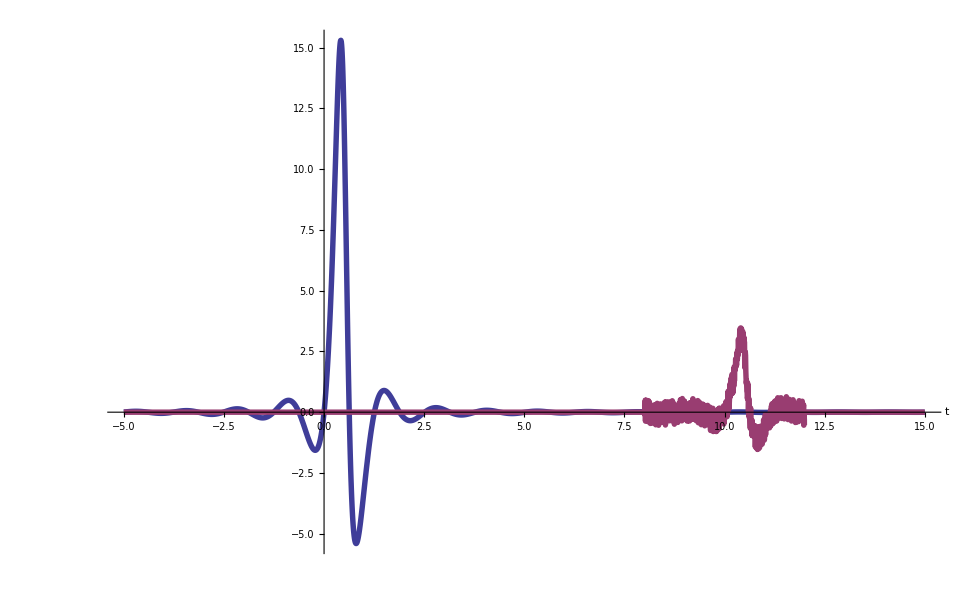

```mathematica
x[t_]:=Sin[5*t]/((t-0.5)^2+0.05);
y[t_]:=(0.2 x[t-10]+RandomReal[]-0.5)* 
UnitStep[(t-8) (12-t)];
Plot[{x[t],y[t]},{t,-5,15},PlotRange->All,
Axes->{True,False},AxesLabel->{"t",None},
PlotStyle->Thickness[0.004],
AxesStyle->Thickness[0.003]]
Clear[x,y]
```